```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

## Define Beams

```mathematica
spectDBWC1={{1,-0.6},{1,0.6}}
spectDBWC2={{0.5,-0.6},{1,0.6}}
spectDBWC3={{0.1,-0.6},{1,0.6}}
```

{{1,-0.6},{1,0.6}}

{{0.5,-0.6},{1,0.6}}

{{0.1,-0.6},{1,0.6}}

```mathematica
spectDBC1={{-1,-0.6},{1,0.6}}
spectDBC2={{-0.5,-0.6},{1,0.6}}
spectDBC3={{-0.1,-0.6},{1,0.6}}
```

{{-1,-0.6},{1,0.6}}

{{-0.5,-0.6},{1,0.6}}

{{-0.1,-0.6},{1,0.6}}

## Define Useful Functions

```mathematica
DBPltDRMAA[spect_,pltRange_:{{-2,2},{-2,2}}]:=Module[{spectM},

spectM=spect;

ParametricPlot[
{DBAxialSymKNMAA[spectM, n],DBAxialSymOmegaNMAA[spectM, n]},
{n,-50,50},
PlotRange->pltRange,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltDRMAAData[spect_,discret_:0.01]:=Module[{spectM},

spectM=spect;

Table[
{DBAxialSymKNMAA[spectM, n],DBAxialSymOmegaNMAA[spectM, n]},
{n,-50,50,discret}
]
]
```

```mathematica
DBPltDRMZA[spect_,pltRange_:{{-2,2},{-2,2}}]:=Module[{spectM},

spectM=spect;

ParametricPlot[
Evaluate[
{n #, #} &/@DBAxialSymOmegaNMZA[spectM, n]
],
{n,-50,50},
PlotRange->pltRange,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"},PlotLegends->Placed[{"MZA+","MZA-"},{Above,Center}]
]
]
```

```mathematica
DBPltDRMZAData[spect_,discret_:0.01]:=Module[{spectM},

spectM=spect;

Table[
Evaluate[
{n #, #} &/@DBAxialSymOmegaNMZA[spectM, n]
],{n,-50,50,discret}
]

]
```

```mathematica
DBPltOmegaN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymOmegaNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"ω(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltKN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymKNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"k(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
pltDROmegaRealLSA[data_,drplot_]:=Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@data,VertexColors->colorf/@Rescale@(Abs@#[[3]]&/@data)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@data),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega.real"},PlotLabel->"LSA for real ω",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
drplot
]
```

```mathematica
pltDRKRealLSA[data_,drplot_]:=Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@data,VertexColors->colorf/@Rescale@(Abs@#[[3]]&/@data)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@data),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega.real"},PlotLabel->"LSA for real k",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
drplot
]
```

## Calculate DR

```mathematica
spectDBC2
```

{{-0.5,-0.6},{1,0.6}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

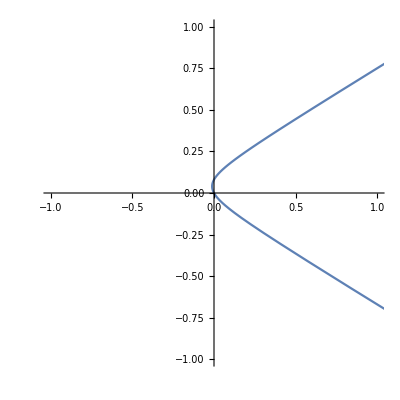

```mathematica
ParametricPlot[
{n DBAxialSymOmegaNMAA[spectDBC2,n],DBAxialSymOmegaNMAA[spectDBC2,n]},
{n,1/spectDBC2[[1,2]],1/spectDBC2[[2,2]]},PlotRange->{{-1,1},{-1,1}}
]
```

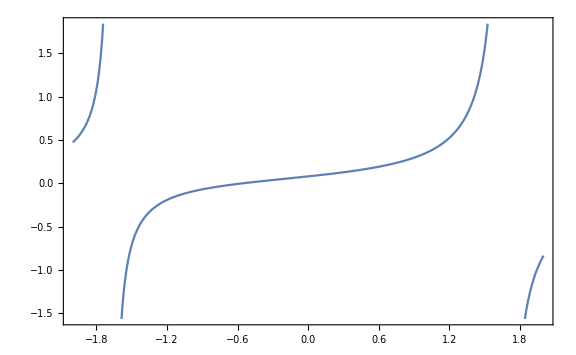

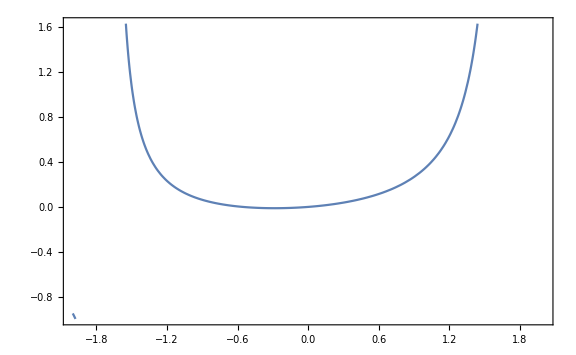

```mathematica
Plot[
DBAxialSymOmegaNMAA[spectDBC2,n],
{n,-2,2},Exclusions->{1/spectDBC2[[1,2]],1/spectDBC2[[2,2]]},Frame->True,ImageSize->Large
]

Plot[
DBAxialSymKNMAA[spectDBC2,n],
{n,-2,2},Exclusions->{1/spectDBC2[[1,2]],1/spectDBC2[[2,2]]},Frame->True,ImageSize->Large
]
```

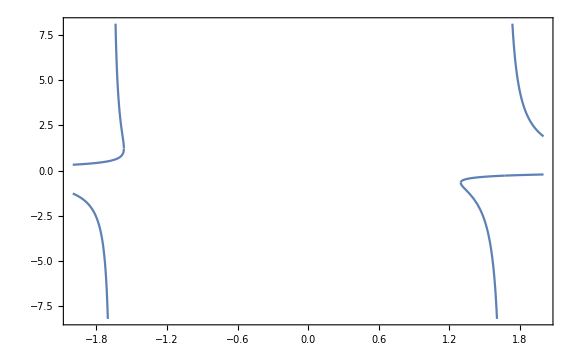

```mathematica
Plot[
DBAxialSymOmegaNMZA[spectDBC2,n],
{n,-2,2},Frame->True,ImageSize->Large,Exclusions->{1/spectDBC1[[1,2]],1/spectDBC1[[2,2]]},ExclusionsStyle->Dashed
]
```

### Export Data For Future Use

#### WC1

Generate the DR plot data

```mathematica
spectDBWC1DRDBPltData=DBPltDRMAAData[spectDBWC1,0.01];
spectDBWC1DRDBMZAPltData=Flatten[DBPltDRMZAData[spectDBWC1,0.01],1];
```

```mathematica
Dimensions@spectDBWC1DRDBPltData
Dimensions@spectDBWC1DRDBMZAPltData
```

{10001,2}

{20002,2}

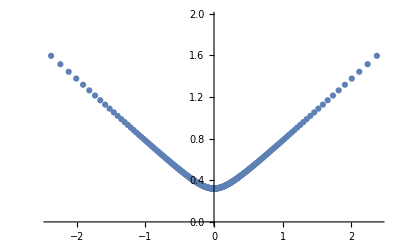

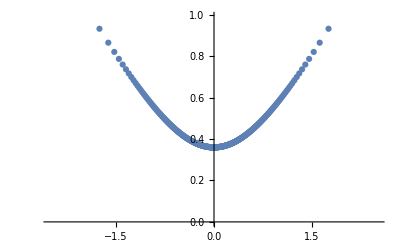

```mathematica
ListPlot[
Sort[Select[spectDBWC1DRDBPltData,#[[2]]>0&],#1[[1]]<#2[[2]]&]
]
ListPlot[
Sort[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&#[[2]]>0&],#1[[1]]<#2[[2]]&]
]
```

```mathematica
spectDBWC1DRDBPltData
```

```mathematica
Export["export/dr-db-two-beams/spectDBWC1DRDBPltData-upper.csv",Sort[Select[spectDBWC1DRDBPltData,#[[2]]>0&],#1[[1]]<#2[[1]]&] 
]
Export["export/dr-db-two-beams/spectDBWC1DRDBPltData-lower.csv",Sort[Select[spectDBWC1DRDBPltData,#[[2]]<0&],#1[[1]]<#2[[1]]&]
]

Export["export/dr-db-two-beams/spectDBWC1DRDBMZAPltData-upper.csv",Sort[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&#[[2]]>0&],#1[[1]]<#2[[1]]&]
]

Export["export/dr-db-two-beams/spectDBWC1DRDBMZAPltData-lower.csv",Sort[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&#[[2]]<0&],#1[[1]]<#2[[1]]&]
]
```

export/dr-db-two-beams/spectDBWC1DRDBPltData-upper.csv

export/dr-db-two-beams/spectDBWC1DRDBPltData-lower.csv

export/dr-db-two-beams/spectDBWC1DRDBMZAPltData-upper.csv

export/dr-db-two-beams/spectDBWC1DRDBMZAPltData-lower.csv

```mathematica
Export["export/dr-db-two-beams/lsaMAARODataDBWC1.csv",lsaMAARODataDBWC1 ]
Export["export/dr-db-two-beams/lsaMZApRODataDBWC1.csv",Select[lsaMZApRODataDBWC1,#[[1]]<0&] ]
Export["export/dr-db-two-beams/lsaMZAmRODataDBWC1.csv",Select[lsaMZAmRODataDBWC1,#[[1]]>0&] ]
```

export/dr-db-two-beams/lsaMAARODataDBWC1.csv

export/dr-db-two-beams/lsaMZApRODataDBWC1.csv

export/dr-db-two-beams/lsaMZAmRODataDBWC1.csv

#### C1

```mathematica
spectDBC1DRDBPltData=DBPltDRMAAData[spectDBC1,0.01];
spectDBC1DRDBMZAPltData=Flatten[DBPltDRMZAData[spectDBC1,0.01],1];
```

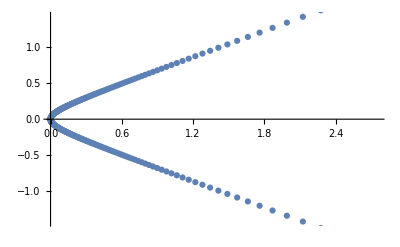

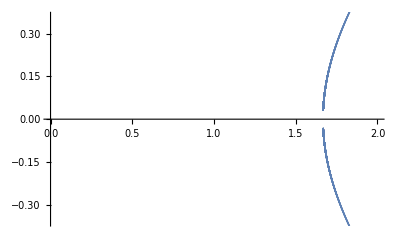

```mathematica
ListPlot[
Sort[Select[spectDBC1DRDBPltData,#[[1]]>0&],#1[[1]]<#2[[1]]&]
]
ListPlot[
Sort[Select[spectDBC1DRDBMZAPltData,#[[2]]∈Reals&&#[[1]]>-0.1&],#1[[1]]<#2[[2]]&],PlotRange->{{0,2},Automatic}
]
```

```mathematica
Export["export/dr-db-two-beams/spectDBC1DRDBPltData-upper.csv",Sort[Select[spectDBC1DRDBPltData,#[[1]]>0&],#1[[2]]<#2[[2]]&] 
]
Export["export/dr-db-two-beams/spectDBC1DRDBPltData-lower.csv",Sort[Select[spectDBC1DRDBPltData,#[[1]]<0&],#1[[2]]<#2[[2]]&]
]

Export["export/dr-db-two-beams/spectDBC1DRDBMZAPltData-upper.csv",Sort[Select[spectDBC1DRDBMZAPltData,#[[2]]∈Reals&&#[[1]]>0&],#1[[2]]<#2[[2]]&]
]

Export["export/dr-db-two-beams/spectDBC1DRDBMZAPltData-lower.csv",Sort[Select[spectDBC1DRDBMZAPltData,#[[2]]∈Reals&&#[[1]]<0&],#1[[2]]<#2[[2]]&]
]
```

export/dr-db-two-beams/spectDBC1DRDBPltData-upper.csv

export/dr-db-two-beams/spectDBC1DRDBPltData-lower.csv

export/dr-db-two-beams/spectDBC1DRDBMZAPltData-upper.csv

export/dr-db-two-beams/spectDBC1DRDBMZAPltData-lower.csv

```mathematica
Export["export/dr-db-two-beams/lsaMAARODataDBC1.csv",Select[lsaMAARODataDBC1,#[[1]]>0&]]
Export["export/dr-db-two-beams/lsaMZApRODataDBC1.csv",Select[lsaMZApRODataDBC1,#[[1]]>0&]]
Export["export/dr-db-two-beams/lsaMZAmRODataDBC1.csv",Select[lsaMZAmRODataDBC1,#[[1]]>0&]]
```

export/dr-db-two-beams/lsaMAARODataDBC1.csv

export/dr-db-two-beams/lsaMZApRODataDBC1.csv

export/dr-db-two-beams/lsaMZAmRODataDBC1.csv

Plots

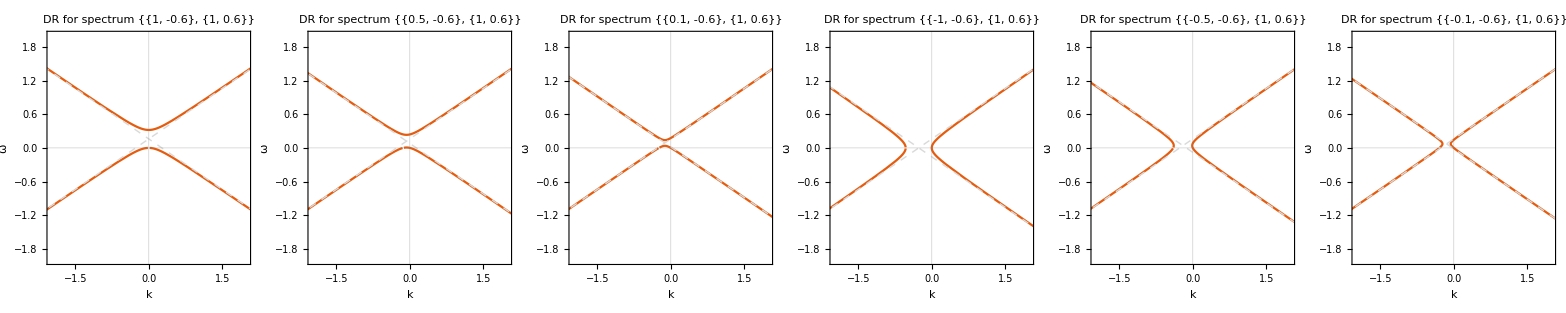

```mathematica
Grid@{
{pltDRMAADBWC1,pltDRMAADBWC2,pltDRMAADBWC3,pltDRMAADBC1,pltDRMAADBC2,pltDRMAADBC3}=Table[
DBPltDRMAA[spectra,{{-2,2},{-2,2}}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
]
}
```

```mathematica
Grid@{
{pltDRMZADBWC1,pltDRMZADBWC2,pltDRMZADBWC3,pltDRMZADBC1,pltDRMZADBC2,pltDRMZADBC3}=Table[
DBPltDRMZA[spectra,{{-4,4},{-4,4}}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
]
}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Calculate Instability

Real Omega MAA

```mathematica
Table[
Symbol["lsaMAARODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAARODataDBWC1,lsaMAARODataDBWC2,lsaMAARODataDBWC3,lsaMAARODataDBC1,lsaMAARODataDBC2,lsaMAARODataDBC3}

```mathematica
{lsaMAARODataRawDBWC1,lsaMAARODataRawDBWC2,lsaMAARODataRawDBWC3,lsaMAARODataRawDBC1,lsaMAARODataRawDBC2,lsaMAARODataRawDBC3} = Table[
LSAMAARODataRawDB[spectra,{-4,4,0.01}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
lsaMAARODataDBList=Table[
LSAMAARODataDB[Symbol["lsaMAARODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
{lsaMAARODataDBWC1,lsaMAARODataDBWC2,lsaMAARODataDBWC3,lsaMAARODataDBC1,lsaMAARODataDBC2,lsaMAARODataDBC3}=lsaMAARODataDBList;
```

```mathematica
lsaMAAROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMAARODataDB"<>spectraid],Symbol["pltDRMAADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMAAROPltDBList[[;;]]}
```

-Graphics-

```mathematica
(*Export["lsaMAAROPltDB-C1-to-C3.png",Out[69]]*)
```

Real Omega MZAp

```mathematica
LSAMZApRODataRawDB[spectDBC1,{-0.1,0.1,0.01}]
```

Power::infy: Infinite expression 1/0. encountered.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{-0.1,-0.612189-1.10599×10^-21 ⅈ},{-0.09,-0.609883+1.05338×10^-15 ⅈ},{-0.08,-0.607816-1.10441×10^-27 ⅈ},{-0.07,-0.605989-1.36314×10^-21 ⅈ},{-0.06,-0.604403-4.35653×10^-22 ⅈ},{-0.05,-0.60306+3.1405×10^-21 ⅈ},{-0.04,-0.601959+1.64984×10^-23 ⅈ},{-0.03,-0.601102-2.29969×10^-26 ⅈ},{-0.02,-0.60049+3.68109×10^-20 ⅈ},{-0.01,-0.600123-7.53348×10^-24 ⅈ},{0.,0.+0.1 ⅈ},{0.01,-4.1473×10^-16+0.22366 ⅈ},{0.02,-1.05471×10^-15+0.238766 ⅈ},{0.03,-4.5048×10^-16+0.265708 ⅈ},{0.04,-1.20179×10^-15+0.307353 ⅈ},{0.05,-1.0376×10^-16+0.368467 ⅈ},{0.06,-2.7636×10^-15+0.456904 ⅈ},{0.07,-1.21342×10^-16+0.58626 ⅈ},{0.08,-4.19341×10^-15+0.78192 ⅈ},{0.09,-2.70635×10^-15+1.09481 ⅈ},{0.1,-3.06062×10^-15+1.66339 ⅈ}}

Generate the variable names

```mathematica
Table[
Symbol["lsaMZApRODataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRODataRawDBWC1,lsaMZApRODataRawDBWC2,lsaMZApRODataRawDBWC3,lsaMZApRODataRawDBC1,lsaMZApRODataRawDBC2,lsaMZApRODataRawDBC3}

```mathematica
Table[
Symbol["lsaMZApRODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRODataDBWC1,lsaMZApRODataDBWC2,lsaMZApRODataDBWC3,lsaMZApRODataDBC1,lsaMZApRODataDBC2,lsaMZApRODataDBC3}

Calculate the instabilities

```mathematica
{lsaMZApRODataRawDBWC1,lsaMZApRODataRawDBWC2,lsaMZApRODataRawDBWC3,lsaMZApRODataRawDBC1,lsaMZApRODataRawDBC2,lsaMZApRODataRawDBC3}= Table[
LSAMZApRODataRawDB[spectra,{-4,4,0.01}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
lsaMZApRODataDBList=Table[
LSAMZApRODataDB[Symbol["lsaMZApRODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] , 0.01,0.01],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
{lsaMZApRODataDBWC1,lsaMZApRODataDBWC2,lsaMZApRODataDBWC3,lsaMZApRODataDBC1,lsaMZApRODataDBC2,lsaMZApRODataDBC3}=lsaMZApRODataDBList;
```

```mathematica
lsaMZApROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMZApRODataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMZApROPltDBList[[;;3]],lsaMZApROPltDBList[[4;;]]}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZApROPltDB-C1-to-C3.png",Out[105]]*)
```

Real Omega MZAm

Generate the variable names

```mathematica
Table[
Symbol["lsaMZAmRODataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRODataRawDBWC1,lsaMZAmRODataRawDBWC2,lsaMZAmRODataRawDBWC3,lsaMZAmRODataRawDBC1,lsaMZAmRODataRawDBC2,lsaMZAmRODataRawDBC3}

```mathematica
Table[
Symbol["lsaMZAmRODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRODataDBWC1,lsaMZAmRODataDBWC2,lsaMZAmRODataDBWC3,lsaMZAmRODataDBC1,lsaMZAmRODataDBC2,lsaMZAmRODataDBC3}

Calculate the instabilities

```mathematica
{lsaMZAmRODataRawDBWC1,lsaMZAmRODataRawDBWC2,lsaMZAmRODataRawDBWC3,lsaMZAmRODataRawDBC1,lsaMZAmRODataRawDBC2,lsaMZAmRODataRawDBC3}= Table[
LSAMZAmRODataRawDB[spectra,{-4,4,0.01}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
lsaMZAmRODataDBList=Table[
LSAMZAmRODataDB[Symbol["lsaMZAmRODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.01],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
{lsaMZAmRODataDBWC1,lsaMZAmRODataDBWC2,lsaMZAmRODataDBWC3,lsaMZAmRODataDBC1,lsaMZAmRODataDBC2,lsaMZAmRODataDBC3}=lsaMZAmRODataDBList;
```

```mathematica
lsaMZAmROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMZAmRODataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMZAmROPltDBList[[;;3]],lsaMZAmROPltDBList[[4;;]]}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZAmROPltDB-C1-to-C3.png",Out[125]]*)
```

Real k MAA

Generate the variable names for real k (MAA) solution

```mathematica
Table[
Symbol["lsaMAARKDataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAARKDataRawDBWC1,lsaMAARKDataRawDBWC2,lsaMAARKDataRawDBWC3,lsaMAARKDataRawDBC1,lsaMAARKDataRawDBC2,lsaMAARKDataRawDBC3}

```mathematica
Table[
Symbol["lsaMAARKDataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAARKDataDBWC1,lsaMAARKDataDBWC2,lsaMAARKDataDBWC3,lsaMAARKDataDBC1,lsaMAARKDataDBC2,lsaMAARKDataDBC3}

Calculate the instabilities

```mathematica
{lsaMAARKDataRawDBWC1,lsaMAARKDataRawDBWC2,lsaMAARKDataRawDBWC3,lsaMAARKDataRawDBC1,lsaMAARKDataRawDBC2,lsaMAARKDataRawDBC3}= Table[
LSAMAARKDataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

```mathematica
lsaMAARKDataDBList=Table[
LSAMAARKDataDB[Symbol["lsaMAARKDataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.01],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMAARKDataDBWC1,lsaMAARKDataDBWC2,lsaMAARKDataDBWC3,lsaMAARKDataDBC1,lsaMAARKDataDBC2,lsaMAARKDataDBC3}=lsaMAARKDataDBList;
```

```mathematica
lsaMAARKPltDBList=Table[
pltDRKRealLSA[
Symbol["lsaMAARKDataDB"<>spectraid],Symbol["pltDRMAADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMAARKPltDBList[[;;3]],lsaMAARKPltDBList[[4;;]]}
```

-Graphics-

```mathematica
(*Export["lsaMAARKPltDB-WC1-to-WC3-and-C1-to-C3.png",Out[212]]*)
```

Real k MZAp

```mathematica
Table[
Symbol["lsaMZApRKDataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRKDataRawDBWC1,lsaMZApRKDataRawDBWC2,lsaMZApRKDataRawDBWC3,lsaMZApRKDataRawDBC1,lsaMZApRKDataRawDBC2,lsaMZApRKDataRawDBC3}

```mathematica
Table[
Symbol["lsaMZApRKDataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRKDataDBWC1,lsaMZApRKDataDBWC2,lsaMZApRKDataDBWC3,lsaMZApRKDataDBC1,lsaMZApRKDataDBC2,lsaMZApRKDataDBC3}

Calculate the instabilities

```mathematica
{lsaMZApRKDataRawDBWC1,lsaMZApRKDataRawDBWC2,lsaMZApRKDataRawDBWC3,lsaMZApRKDataRawDBC1,lsaMZApRKDataRawDBC2,lsaMZApRKDataRawDBC3}= Table[
LSAMZApRKDataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

Last::normal: Nonatomic expression expected at position 1 in Last[omega].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

```mathematica
lsaMZApRKDataDBList=Table[
LSAMZApRKDataDB[Symbol["lsaMZApRKDataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.001],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMZApRKDataDBWC1,lsaMZApRKDataDBWC2,lsaMZApRKDataDBWC3,lsaMZApRKDataDBC1,lsaMZApRKDataDBC2,lsaMZApRKDataDBC3}=lsaMZApRKDataDBList;
```

```mathematica
lsaMZApRKPltDBList=Table[
pltDRKRealLSA[
Symbol["lsaMZApRKDataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMZApRKPltDBList[[;;3]],lsaMZApRKPltDBList[[4;;]]}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZApRKPltDB-WC1-to-WC3-and-C1-to-C3.png",Out[263]]*)
```

Real k MZAm

```mathematica
Table[
Symbol["lsaMZAmRKDataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRKDataRawDBWC1,lsaMZAmRKDataRawDBWC2,lsaMZAmRKDataRawDBWC3,lsaMZAmRKDataRawDBC1,lsaMZAmRKDataRawDBC2,lsaMZAmRKDataRawDBC3}

```mathematica
Table[
Symbol["lsaMZAmRKDataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRKDataDBWC1,lsaMZAmRKDataDBWC2,lsaMZAmRKDataDBWC3,lsaMZAmRKDataDBC1,lsaMZAmRKDataDBC2,lsaMZAmRKDataDBC3}

Calculate the instabilities

```mathematica
{lsaMZAmRKDataRawDBWC1,lsaMZAmRKDataRawDBWC2,lsaMZAmRKDataRawDBWC3,lsaMZAmRKDataRawDBC1,lsaMZAmRKDataRawDBC2,lsaMZAmRKDataRawDBC3}= Table[
LSAMZAmRKDataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

Last::normal: Nonatomic expression expected at position 1 in Last[omega].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

```mathematica
lsaMZAmRKDataDBList=Table[
LSAMZAmRKDataDB[Symbol["lsaMZAmRKDataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.001],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMZAmRKDataDBWC1,lsaMZAmRKDataDBWC2,lsaMZAmRKDataDBWC3,lsaMZAmRKDataDBC1,lsaMZAmRKDataDBC2,lsaMZAmRKDataDBC3}=lsaMZAmRKDataDBList;
```

```mathematica
lsaMZAmRKPltDBList=Table[
pltDRKRealLSA[
Symbol["lsaMZAmRKDataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMZAmRKPltDBList[[;;3]],lsaMZAmRKPltDBList[[4;;]]}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZAmRKPltDB-WC1-to-WC3-and-C1-to-C3.png",Out[273]]*)
```

## Complex omega and k

MAA

```mathematica
Table[
Symbol["lsaMAADataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAADataRawDBWC1,lsaMAADataRawDBWC2,lsaMAADataRawDBWC3,lsaMAADataRawDBC1,lsaMAADataRawDBC2,lsaMAADataRawDBC3}

```mathematica
Table[
Symbol["lsaMAADataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAADataDBWC1,lsaMAADataDBWC2,lsaMAADataDBWC3,lsaMAADataDBC1,lsaMAADataDBC2,lsaMAADataDBC3}

```mathematica
LSAMAADataRawDBTEST[spect_,omegarange_:{{-4,4,0.01},{-4,4,0.01}}]:=Module[{kMAAFunM,dataM,baddataM},

kMAAFunM[omega_]:=Last[
k/.Solve[
DBAxialSymOmegaNMAAEqnLHSComplex[omega,k,spect]==0,
k
]
];

dataM=Table[
	{
		omegareal+omegaimag*I,kMAAFunM[omegareal+omegaimag*I]
	},
	{omegareal,omegarange[[1,1]],omegarange[[1,2]],omegarange[[1,3]]},
	{omegaimag,omegarange[[2,1]],omegarange[[2,2]],omegarange[[2,3]]}
];

(*baddataM[entry_]:=Not[MatchQ[entry,{_?NumberQ,_?NumberQ}]];*)

(*DeleteCases[dataM,_?baddataM]*)

dataM

];
```

```mathematica
lsaMAAComplexOKDBC1=LSAMAADataRawDB[spectDBC1,{{-4,4,0.1},{-4,4,0.1}}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

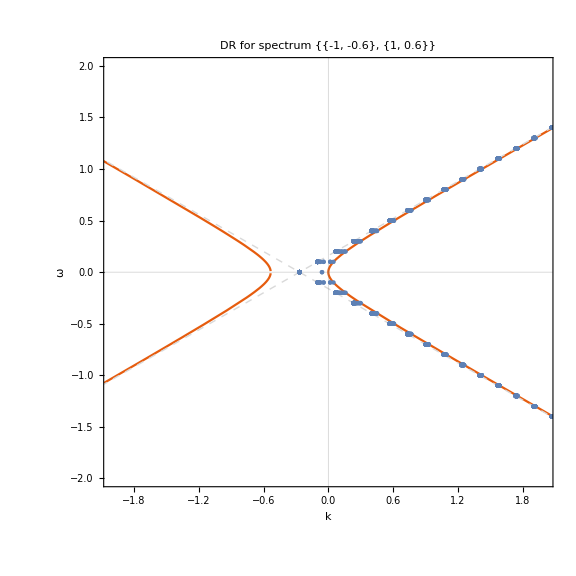

```mathematica
Show[
pltDRMAADBC1,
ListPlot[
{Re@#[[2]],Re@#[[1]]}&/@Flatten[lsaMAAComplexOKDBC1,1]
]
]
```

MAA

```mathematica
Table[
Symbol["lsaMAADataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAADataRawDBWC1,lsaMAADataRawDBWC2,lsaMAADataRawDBWC3,lsaMAADataRawDBC1,lsaMAADataRawDBC2,lsaMAADataRawDBC3}

```mathematica
Table[
Symbol["lsaMAADataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAADataDBWC1,lsaMAADataDBWC2,lsaMAADataDBWC3,lsaMAADataDBC1,lsaMAADataDBC2,lsaMAADataDBC3}

```mathematica
lsaMAAComplexOKDBC1=LSAMAADataRawDB[spectDBC1,{{-4,4,0.1},{-4,4,0.1}}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

```mathematica
Show[
pltDRMAADBC1,
ListPlot[
{Re@#[[2]],Re@#[[1]]}&/@Flatten[lsaMAAComplexOKDBC1,1]
]
]
```

-Graphics-

```mathematica
lsaMZApComplexOKDBC1=LSAMZApDataRawDB[spectDBC1,{{-4,4,0.1},{-4,4,0.1}}];
```

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Last::normal: Nonatomic expression expected at position 1 in Last[k].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

```mathematica
Show[
pltDRMZADBC1,
ListPlot[
{Re@#[[2]],Re@#[[1]]}&/@Flatten[lsaMZApComplexOKDBC1,1]
]
]
```

-Graphics-

```mathematica
lsaMZAmComplexOKDBC1=LSAMZAmDataRawDB[spectDBC1,{{-2,2,0.1},{-4,4,0.1}}];
```

Last::normal: Nonatomic expression expected at position 1 in Last[k].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

```mathematica
Show[
pltDRMZADBC1,
ListPlot[
{Re@#[[2]],Re@#[[1]]}&/@Flatten[lsaMZAmComplexOKDBC1,1]
]
]
```

-Graphics-